```mathematica
kOdd:=(2π n)/L0 -(2 π^3 n^3 α δ^2)/L0^2;
kEven:=(2π n)/L0+1/(2π n)1/(α/4+L0/(2π n)^2) +(2 π^3 n^3 α δ^2)/L0^2
```

```mathematica
Delta1:=1/(4π n)1/(α/4+L0/(2π n)^2)
```

```mathematica
beta1:=2*Delta1*(2 π^3 n^3 α)/L0^2
```

```mathematica
kOdd1:=(2π n)/L0 +Delta1-Sqrt[Delta1^2+beta1*δ^2];
kEven1:=(2π n)/L0 +Delta1+Sqrt[Delta1^2+beta1*δ^2];
```

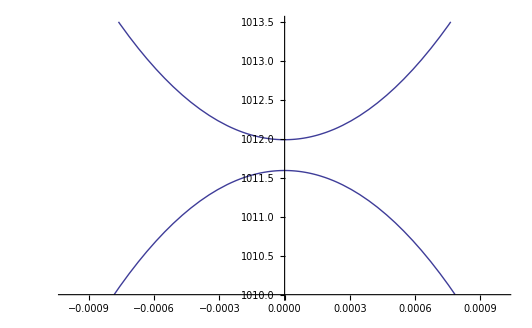

```mathematica
pic1=Plot[{L0*kOdd,L0*kEven}/.{L0->10^-4,n->161,α->   10^-6},{δ,-0.001,0.001},PlotRange->{1010,1013.5}]
```

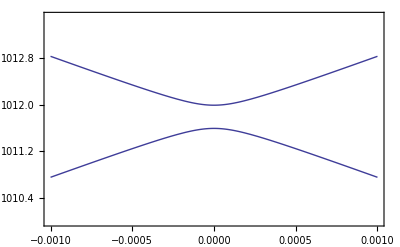

```mathematica
pic2=Plot[{L0*kOdd1,L0*kEven1}/.{L0->10^-4,n->161,α->   10^-6},{δ,-0.001,0.001},PlotRange->{1010,1013.5},Frame->True,Axes->False,PlotStyle->Thick]
```

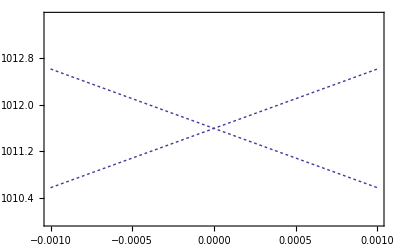

```mathematica
pic3=Plot[{2*Pi*n/(1+δ),2*Pi*n/(1-δ)}/.{L0->10^-4,n->161,α->   10^-6},{δ,-0.001,0.001},PlotRange->{1010,1013.5},Frame->True,Axes->False,PlotStyle->{Dashing[Tiny]}]
```

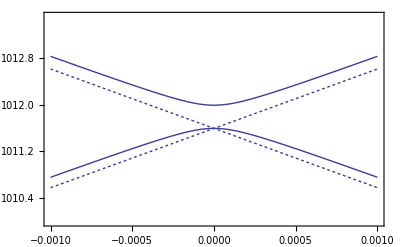

```mathematica
pic4=Show[pic2,pic3]
```